```mathematica
SetDirectory[NotebookDirectory[]]
Needs["SSS`"]
```

C:\Users\caviness\Documents\Git\SSS-Code\Main

## Functions that generate lists of integers, and function to ID sessie network

### Explanations

MaxStateLengthPositions, LeastUsedRulePositions, DistanceTally, DistanceLastPositions

#### MaxStateLengthPositions: positions in "Evolution" where a new maximum state string length is reached for the first time

#### LeastUsedRulePositions: positions where the least-used rule was used

#### Note: both of these functions call a filtering function, MergeIntervalsByRulesUsed, which verifies that the same rules are used in each interval between positions in the list, and may discard unimportant positions.

#### DistanceLastPositions: a list containing, for each positive integer n, the position of the last nodes that is n steps from origin on the undirected graph of "Net".

Note: these first three provide lists of numbers based sessie events / network nodes, so as soon as a "Verdict" has been assigned, the CheckDimensions summaries can be used by GuessDimension and TestForUnusedRules.

#### DistanceTally: number of nodes in the undirected graph of "Net" that are no more than 1, 2, 3, ... steps from origin. (SSSAnimate[sss, VertexLabels → "VertexWeight"] gives a related, helpful visualization.)

#### CheckDimensions: accepts a list of "significant" positive integers, returns {"1D"|"2D"|...|"exp", n, {k, delay, matchlen, match}, dt}, indicating an n-dimensional or exponential network. Pattern detection required k-averaging, and a delay before the pattern was established and a difference or ratio match of length matchlen was detected. The difference table dt is provided for human inspection, but in theory it (but not the network) could be summarized as {n, dt⟦All, delay;;delay+k⟧} or {"exp", dt⟦All, delay;;delay+k⟧}, respectively. (In fact, only the first element of each row is needed, until the final row.) It is not currently clear whether k and match have any useful meaning in the exponential summary, but both can be reconstructed from the difference table summary. The function GuessDimension collects IDs ("1D", "2D", etc.) returned for any of the 4 significant number generator functions, and considers matchlen as a measure of reliability.

#### GuessDimension: with appropriate checks, tries all 4 approximative tests by applying CheckDimensions to the lists described above. Sessie is auto-extended to try to reach agreement. Changes "Verdict" if the combined matchlen values returned indicate satisfactory reliability.

#### TestForUnusedRules: decides whether to skip this case, and whether a long-jump is possible, once the sessie or the net has been identified (as "Repeating" or otherwise by GuessDimension).

#### Possible issues & notes:

(1) If dt⟦1,1⟧ == j ≠ 1, there was some initial stuff before the pattern set in.

Solution: If the numbers were provided by either MaxStateLengthPositions or LeastUsedRulePositions, toss out the first j-1 steps of the sessie to generate a network with a difference table in which the first j-1 columns are dropped, and the first row entries are all reduced by subtracting j-1.  If the numbers were produced from the "Net", it's unclear how much of the sessie state strings should be skipped.

(2) Once reliable ID has been made, call TestForUnusedRules to decide whether to skip this case, and whether a long-jump is possible:  affects acceleration.  Later call ImproveInitialState (not yet written), to discard initial or final tagged cells unchanged by the evolution:  only affects sessie display, not the network.  Think carefully about unchanged interior tagged cells:  removing an inert cell might allow a different evolution.

(*) Once we have a network summary...:  Depending on the initial state string, a different network summary might be generated:  how to recognize their equivalence?

Possible solution: Make k alternative summaries, treating by dropping 0, 1, …, k-1 states [as in (1)], sort them (perhaps by last row, then next-to-last, etc.), treat as "canonical" the first in the sorted list.

### Code

```mathematica
LeastUsedRulePositions[sss_Association /; KeyExistsQ[sss,"RulesUsed"]] := Module[{ru=sss["RulesUsed"],len,ruletally,least},
len=Length[ru];
ruletally=Tally[ru⟦Round[.1len];;len⟧];      (* skip 10% of rules used, tally the rest *)
least=First@First@SortBy[ruletally,Last];  (* identify the least used rule *)
MergeIntervalsByRulesUsed[Flatten@Position[ru,least],ru]  (* find its occurrences anywhere, merge intervals & return *) 
];
```

```mathematica
LeastUsedRulePositions::usage = "Takes sss, an already generated sessie object, and returns the list of positions where the least-used rule was applied (least-used in the last 90% of the evolution).  This list is modified by the function MergeIntervalsByRulesUsed before being returned.";
```

```mathematica
MaxStateLengthPositions[sss_Association /; KeyExistsQ[sss,"Evolution"]]:=Module[{currmaxlenstringlen,strlens,strt,evollen,evol=sss["Evolution"],b=Boole[sss["Verdict"]==="Repeating"]},
evollen=Length[evol];
strlens=StringLength /@ evol;
currmaxlenstringlen=Min[strlens];
strt=First@First[Position[strlens,currmaxlenstringlen,1]];
Most@
MergeIntervalsByRulesUsed[
Last@Last@Reap[
Do[
If[StringLength[evol⟦n⟧]>currmaxlenstringlen-b,(* if repeating, "≥" *)
Sow[n]; currmaxlenstringlen=StringLength[evol⟦n⟧]
],
{n,strt,evollen}]
],
sss["RulesUsed"]
]
];
```

```mathematica
MaxStateLengthPositions::usage = "Takes sss, an already generated sessie object, and returns the list of positions where the sessie state string reached a new maximum length, starting with the minimum length string -- which hopefully eliminates some initial non-pattern stuff.  This list is modified by the function MergeIntervalsByRulesUsed before being returned.";
```

```mathematica
MergeIntervalsByRulesUsed[l0_List,ru_List] := Module[{l=l0,n=Length[l0],rulesused1,rulesused2},
(* Expects a list of interesting integers (l0, defining intervals) and the "RulesUsed" list of some SSS.  Merges any intervals in which fewer different rules were used than in neighboring intervals.
Returns the resulting list, which should be more meaningful than the original one. Give up if length ≤ 2 *) 
While[n>2,
rulesused1=Union[ru⟦l⟦n-2⟧;;l⟦n-1⟧-1⟧];
rulesused2=Union[ru⟦l⟦n-1⟧;;l⟦n⟧-1⟧];
(* If[$debug,Print["rules used:", rulesused1,", ",rulesused2]]; *)
Which[
rulesused1==rulesused2, n--,
SubsetQ[rulesused1,rulesused2], l=Drop[l,{n}];n=Length[l],
SubsetQ[rulesused2,rulesused1], l=Drop[l,{n-2}];n=Length[l],
True,l=Drop[l,{n-1}];n=Length[l]
]
];
l]
```

```mathematica
Clear[ReliableDistances];ReliableDistances[sss_Association /; KeyExistsQ[sss,"OutDegreeRemaining"]] := Module[{len,net=sss["Net"],odr,z,eins,pos,distances,maxdistance},
If[Length[net]==0,Return[{}]];  (* no network, no distances! *)
eins=Min[Flatten[net/.Rule->List]];
If[$debug,Print["smallest node in net: ",eins]];
(* Find the end of last case of the longest run of 0s (or least entry) in the list of remaining outdegrees, after skipping first 10% *)
len=Length[sss["OutDegreeRemaining"]];
odr=ReplacePart[sss["OutDegreeRemaining"],_?(#<.1len&)->∞];  (* set first 10% = ∞, these will be ignored *)
If[$debug,Print["OutDegreeRemaining (massaged): ", odr]];
z = Min[odr];  
If[$debug,Print["treating as zero (in odr): ", z]];
(* for our purposes, z will be treated as 0, nodes that are as complete as possible have outdegree remaining = z *)
If[$debug,Print["using \"OutDegreeRemaining\" to find end of reliable data: ",
(odr /. {Longest[g___,1],f:Longest[z..,2],h___}:>{{g},{f},{h}})]];
pos=(odr /. {Longest[g___,1],f:Longest[z..,2],h___}:>Length[{g,f}]+Flatten@Position[{h},_?(#≠0&)]);If[$debug,Print["Position of first untrustworthy node: ", pos]]; 
(* distances = sss["Distance"]; *)   (* now using undirected graph distances... *)
distances = GraphDistance[UndirectedGraph[sss["Net"]],eins];
If[$debug,Print["distances (uncut): ",distances]];
maxdistance=Min[distances⟦pos⟧];
If[$debug,Print["last distance we'll trust: ", maxdistance]];
distances /. _?(#>maxdistance&)->-1  (* replace unreliable distances by -1 *)
];
```

```mathematica
DistanceLastPositions[sss_Association /; KeyExistsQ[sss,"OutDegreeRemaining"]] := 
(* find the position of the last node with (reliable) distance 1, 2, ... *)
Module[{rd=ReliableDistances[sss]},
If[Length[rd]==0,{},
MergeIntervalsByRulesUsed[
Last[Last[Position[rd,#,{1}]]]& /@ Range[Max[Complement[rd,{∞}]]],
sss["RulesUsed"]
]
]
];
DistanceLastPositions::usage = "Takes sss, an already generated sessie object, and returns the list of positions {n_1, n_2, …, n_k} in its causal network, each of which is the last node at the indicated distance from the origin.  Thus n_1 is the node of maximum index which is 1 step away, n_2 the largest that is 2 steps away, etc. But only the final 90% of the network is considered. This list is modified by the function MergeIntervalsByRulesUsed before being returned.";
```

```mathematica
DistanceTally[sss_Association /; KeyExistsQ[sss,"OutDegreeRemaining"]] :=   
(* tally reliable distances, sort, drop the unreliable (-1 & ∞) tally, keep numbers only *) 
Module[{rd=ReliableDistances[sss]},
If[Length[rd]==0,{},
Accumulate[Last /@ Rest@Sort@DeleteCases[Tally[rd],{∞,_}]]
]
];
DistanceTally::usage = "Takes sss, an already generated sessie object, and returns the list of how many nodes are 0 steps from the origin, how many 1 step away, how many 2 steps away, …. But only the final 90% of the network is considered.";
```

```mathematica
LongestPositiveSubsequence[l_List] := Module[{mx,spl},
spl=SplitBy[l/.ComplexInfinity->∞,0≤#<∞&];
mx=Max[Length/@spl];
First[Select[spl,Length[#]==mx&]]
]
```

```mathematica
Clear[RecognizeDifferenceRow];
RecognizeDifferenceRow[l_List] := Module[{len=Length[l],ptrn,dlay,mtch,mtchlen,k,rats},
For[k=1,k≤len/2,k++,  (* for each possible size moving average run k *)
ptrn=MovingAverage[l,k];
(* Print["ptrn: ",ptrn]; *)
If[MatchQ[ptrn,{Repeated[_,{0,5}],Repeated[b_,{5,∞}],Repeated[_,{0,3}]}],
(* accept no more than 5 junk items at the start, no more than 3 at the end, need at least 5 repeated items between *)
{dlay,mtchlen,mtch}=(ptrn/.{a:Repeated[_,{0,5}],brun:Longest[Repeated[b_,{5,∞}]],Repeated[_,{0,3}]}:>{Length[{a}],Length[{brun}],b}); 
Return[{"dim",{k,dlay,mtchlen,mtch}}]  (* constant row found, needed k-averaging, after dlay, including a mtch of length mtchlen *)
];
Off[Divide::infy,Divide::indet];
rats=LongestPositiveSubsequence[Ratios[ptrn]];  (* try ratios instead *)
(* Print["rats: ",rats]; *)
If[MatchQ[rats,{Repeated[_,{0,5}],Repeated[b_?(#>1&),{3,∞}],Repeated[_,{0,3}]}],
(* accept no more than 5 junk items at the start, no more than 3 at the end, need at least 3 repeated positive ratios between *)
{dlay,mtchlen,mtch}=(rats/.{a:Repeated[_,{0,5}],brun:Longest[Repeated[b_?(#>1&),{3,∞}]],Repeated[_,{0,3}]}:>{Length[{a}],Length[{brun}],b});
On[Divide::infy,Divide::indet];
Return[{"exp",{k,dlay,mtchlen,mtch}}] (* exponential, needed k-averaging, after dlay, including a mtch of length mtchlen *)
]
];
{}]  (* {} = failure, {"dim"|"exp", {k, dlay, (max) match length,(diff|ratio)mtch}} = success! *)
```

```mathematica
CheckDimension[l_List]:=Module[{diffsTable={l,Differences[l]},lastrow,ans,k,dlay,mtchlen,mtch},
While[Length[lastrow=Last[diffsTable]]≥5, (* stop when rows become too short *)
ans=RecognizeDifferenceRow[lastrow];  (* try to ID this row *)
If[Length[ans]>0, 
(* success, get details: k-averaging, after dlay, match of length mtchlen *)
{k,dlay,mtchlen,mtch}=ans⟦2⟧;
Return[{
Switch[ans⟦1⟧,
"exp","exp" (* <>ToString[Length[diffsTable]-1] *),
"dim",ToString[Length[diffsTable]-1]<>"D"
],
ans⟦2⟧,
Framed@Grid[diffsTable⟦All,dlay+1;;dlay+k⟧],Grid[diffsTable]}],
(* failure, add another row, try again *)
AppendTo[diffsTable,Differences[Last[diffsTable]]]
]
];
{"failed",Grid[diffsTable]}]
```

```mathematica
Clear[GuessDimension];
SetAttributes[GuessDimension,HoldFirst];
GuessDimension[sss0_] := Module[{len,sss,ans,anssum,vdct,chngd=False,RC},
(* may change the "Verdict" field of the SSS object passed as an argument *)
sss=Evaluate[sss0]; (* local copy to use *)
If[!KeyExistsQ[sss,"Evolution"],Return["Invalid input"]];
If[MatchQ[vdct=sss["Verdict"],"Repeating"|"Dead"], Return[vdct]];

len=Length[sss["RulesUsed"]];
If[$debug,Print["evol len: ", len]];
ans=DeleteCases[
CheckDimension /@ {MaxStateLengthPositions[sss],LeastUsedRulePositions[sss],DistanceLastPositions[sss],DistanceTally[sss]},
{"failed",___}];
(* extract dim & mtchlen, then sort in decreasing order by matchlen *)
anssum=ReverseSortBy[{#⟦1⟧,#⟦2,3⟧}& /@ ans,Last];  
(* gather by dim, total all matchlens *)
anssum={#⟦1,1⟧,Total[Last/@#]}& /@ GatherBy[anssum,First];
If[$debug,Print[anssum]];

While[len<5000 && anssum⟦1,-1⟧<10+5*Length[anssum],(* try for agreement *)
chngd=True;
sss=SSSEvolve[sss,len*Round[(10+5*Length[anssum]-anssum⟦1,-1⟧)/5]];  (* extend the sss evolution a bit, depending *)
len=Length[sss["RulesUsed"]];
If[$debug,Print["evol len: ", len]];
ans=DeleteCases[
CheckDimension /@ {MaxStateLengthPositions[sss],LeastUsedRulePositions[sss],DistanceLastPositions[sss],DistanceTally[sss]},
{"failed",___}];
(* extract dim & mtchlen, then sort in decreasing order by matchlen *)
anssum=ReverseSortBy[{#⟦1⟧,#⟦2,3⟧}& /@ ans,Last];  
(* gather by dim, total all matchlens *)
anssum={#⟦1,1⟧,Total[Last/@#]}& /@ GatherBy[anssum,First];
If[$debug,Print[anssum]];
];
vdct=If[Length[anssum]==1,anssum⟦1,1⟧ (* agree! *), anssum (* disagree *)];  
If[len<5000 , chngd=True; sss["Verdict"]=vdct]; (* trust it *)
If[chngd,sss0=sss]; (* update it if changed *)
Print[vdct];
ans
];
```

### Examples of usage



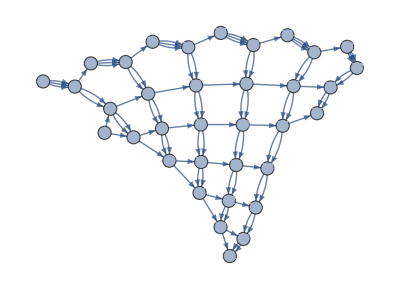
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss90=SSS[{"ABA"->"AAB","A"->"ABA"}, "CAABAD",75,SSSMax->25, NetMax->35,SSSSize->100,NetSize->400, VertexSize->0.6];
```

```mathematica
sss90["RuleSet"]
```

{ABA→AAB,A→ABA}

```mathematica
sss90["Evolution"]
```

{A,ABA,AAB,ABAAB,AABAB,AAABB,ABAAABB,AABAABB,AAABABB,AAAABBB,ABAAAABBB,AABAAABBB,AAABAABBB,AAAABABBB,AAAAABBBB,ABAAAAABBBB,AABAAAABBBB,AAABAAABBBB,AAAABAABBBB,AAAAABABBBB,AAAAAABBBBB,ABAAAAAABBBBB,AABAAAAABBBBB,AAABAAAABBBBB,AAAABAAABBBBB,AAAAABAABBBBB,AAAAAABABBBBB,AAAAAAABBBBBB,ABAAAAAAABBBBBB,AABAAAAAABBBBBB,AAABAAAAABBBBBB,AAAABAAAABBBBBB,AAAAABAAABBBBBB,AAAAAABAABBBBBB,AAAAAAABABBBBBB,AAAAAAAABBBBBBB,ABAAAAAAAABBBBBBB,AABAAAAAAABBBBBBB,AAABAAAAAABBBBBBB,AAAABAAAAABBBBBBB,AAAAABAAAABBBBBBB,AAAAAABAAABBBBBBB,AAAAAAABAABBBBBBB,AAAAAAAABABBBBBBB,AAAAAAAAABBBBBBBB,ABAAAAAAAAABBBBBBBB,AABAAAAAAAABBBBBBBB,AAABAAAAAAABBBBBBBB,AAAABAAAAAABBBBBBBB,AAAAABAAAAABBBBBBBB,AAAAAABAAAABBBBBBBB,AAAAAAABAAABBBBBBBB,AAAAAAAABAABBBBBBBB,AAAAAAAAABABBBBBBBB,AAAAAAAAAABBBBBBBBB,ABAAAAAAAAAABBBBBBBBB,AABAAAAAAAAABBBBBBBBB,AAABAAAAAAAABBBBBBBBB,AAAABAAAAAAABBBBBBBBB,AAAAABAAAAAABBBBBBBBB,AAAAAABAAAAABBBBBBBBB,AAAAAAABAAAABBBBBBBBB,AAAAAAAABAAABBBBBBBBB,AAAAAAAAABAABBBBBBBBB,AAAAAAAAAABABBBBBBBBB,AAAAAAAAAAABBBBBBBBBB,ABAAAAAAAAAAABBBBBBBBBB,AABAAAAAAAAAABBBBBBBBBB,AAABAAAAAAAAABBBBBBBBBB,AAAABAAAAAAAABBBBBBBBBB,AAAAABAAAAAAABBBBBBBBBB,AAAAAABAAAAAABBBBBBBBBB,AAAAAAABAAAAABBBBBBBBBB,AAAAAAAABAAAABBBBBBBBBB,AAAAAAAAABAAABBBBBBBBBB,AAAAAAAAAABAABBBBBBBBBB}

```mathematica
sss90["Net"]
```

{2→3,2→3,2→3,3→4,3→4,1→4,4→5,4→5,1→5,3→6,6→7,6→7,6→7,7→8,7→8,4→8,8→9,8→9,5→9,9→10,9→10,5→10,7→11,11→12,11→12,11→12,12→13,12→13,8→13,13→14,13→14,9→14,14→15,14→15,10→15,15→16,15→16,10→16,12→17,17→18,17→18,17→18,18→19,18→19,13→19,19→20,19→20,14→20,20→21,20→21,15→21,21→22,21→22,16→22,22→23,22→23,16→23,18→24,24→25,24→25,24→25,25→26,25→26,19→26,26→27,26→27,20→27,27→28,27→28,21→28,28→29,28→29,22→29,29→30,29→30,23→30,30→31,30→31,23→31,25→32,32→33,32→33,32→33,33→34,33→34,26→34,34→35,34→35,27→35,35→36,35→36,28→36,36→37,36→37,29→37,37→38,37→38,30→38,38→39,38→39,31→39,39→40,39→40,31→40,33→41,41→42,41→42,41→42,42→43,42→43,34→43,43→44,43→44,35→44,44→45,44→45,36→45,45→46,45→46,37→46,46→47,46→47,38→47,47→48,47→48,39→48,48→49,48→49,40→49,49→50,49→50,40→50,42→51,51→52,51→52,51→52,52→53,52→53,43→53,53→54,53→54,44→54,54→55,54→55,45→55,55→56,55→56,46→56,56→57,56→57,47→57,57→58,57→58,48→58,58→59,58→59,49→59,59→60,59→60,50→60,60→61,60→61,50→61,52→62,62→63,62→63,62→63,63→64,63→64,53→64,64→65,64→65,54→65,65→66,65→66,55→66,66→67,66→67,56→67,67→68,67→68,57→68,68→69,68→69,58→69,69→70,69→70,59→70,70→71,70→71,60→71,71→72,71→72,61→72,72→73,72→73,61→73,63→74,74→75,74→75,74→75}

#### MaxStateLengthPositions: positions in "Evolution" where a new maximum state string length is reached for the first time

```mathematica
MaxStateLengthPositions[sss90]
```

{3,7,12,18,25,33,42,52,63}

Visually, these are the positions in the sessie (colored) image where the state string got longer.

```mathematica
CheckDimension@MaxStateLengthPositions[sss90]
```

{2D,{1,0,7,1},3
4
1,3 | 7 | 12 | 18 | 25 | 33 | 42 | 52 | 63
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }

Identified as (probably) 2-dimensional, pattern valid starting from position 2.  In the 0^th row, provided by MaxStateLengthPositions, we see rapid, increasing growth.  In the row of 1^st differences, growth is linear.  The 2^nd differences row is constant, and the 3^rd differences row would be all 0.  (This is reminiscent of taking derivatives of a quadratic (2^nd-degree) polynomial:  the first derivative is a linear function, the 2^nd is a constant, the 3^rd is zero.

#### LeastUsedRulePositions: positions where the least-used rule was used

```mathematica
LeastUsedRulePositions[sss90]
```

{2,6,11,17,24,32,41,51,62,74}

```mathematica
sss90["RulesUsed"]
```

{1,2,1,1,1,2,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,2,1}

```mathematica
CheckDimension@LeastUsedRulePositions[sss90]
```

{2D,{1,0,8,1},2
4
1,2 | 6 | 11 | 17 | 24 | 32 | 41 | 51 | 62 | 74
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }

Again, the 2nd differences row is constant, indicating 2-d behavior.

#### DistanceLastPositions: a list containing, for each positive integer n, the position of the last node that is n steps from origin on the undirected graph of "Net".

```mathematica
CheckDimension@DistanceLastPositions[sss90]
```

{2D,{1,0,8,1},2
3
1,2 | 5 | 9 | 14 | 20 | 27 | 35 | 44 | 54 | 65
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }

#### DistanceTally: number of nodes in the undirected graph of "Net" that are no more than 1, 2, 3, ... steps from origin. (SSSAnimate[sss, VertexLabels → "VertexWeight"] gives a related, helpful visualization for the directed graph.)

```mathematica
CheckDimension@DistanceTally[sss90]
```

{2D,{1,3,6,1},7
5
1,1 | 2 | 4 | 7 | 12 | 18 | 25 | 33 | 42 | 52 | 63
1 | 2 | 3 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 
1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 |  | }

```mathematica
SSSAnimate[sss90,VertexLabels->"VertexWeight",NetSize->400]
```

#### GuessDimension: tries all 4 approximative tests, with appropriate checks, changes "Verdict" if appropriate.

```mathematica
GuessDimension[sss90]
```

2D

{{2D,{1,0,8,1},2
2
1,2 | 4 | 7 | 11 | 16 | 22 | 29 | 37 | 46 | 56
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{2D,{1,0,9,1},1
2
1,1 | 3 | 6 | 10 | 15 | 21 | 28 | 36 | 45 | 55 | 66
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{2D,{1,0,8,1},2
3
1,2 | 5 | 9 | 14 | 20 | 27 | 35 | 44 | 54 | 65
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{2D,{1,3,6,1},7
5
1,1 | 2 | 4 | 7 | 12 | 18 | 25 | 33 | 42 | 52 | 63
1 | 2 | 3 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 
1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 |  | }}

```mathematica
sss90["Verdict"]
```

2D

```mathematica
TestForUnusedRules[sss90]
```

{}

#### Other examples:

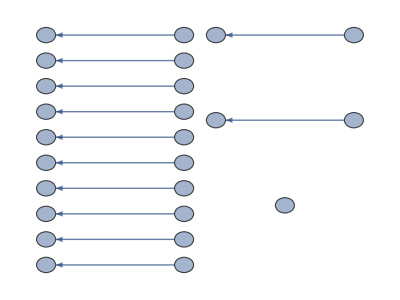
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

Repeating

```mathematica
sss1a=SSS[{"A"->"",""->"A"},"",25,SSSSize->{50,200},NetSize->{400,300}, VertexSize->0.6];
sss1a["Verdict"]
```

```mathematica
CheckDimension@LeastUsedRulePositions[sss1a]
```

{1D,{1,0,11,2},2
2,2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | }

```mathematica
CheckDimension@MaxStateLengthPositions[sss1a]
```

{1D,{1,0,11,2},2
2,2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | }

```mathematica
CheckDimension@DistanceLastPositions[sss1a]
```

{failed,2
}

```mathematica
CheckDimension@DistanceTally[sss1a]
```

{failed,1
}

```mathematica
GuessDimension[sss1a]
```

Repeating

```mathematica
TestForUnusedRules[sss1a]
```

{}

If the sessie is disconnected, neither DistanceTally nor DistanceLastPositions may generate a usable list.  But fortunately, any repeating sessie can automatically be assumed to have dimension 1.   This is supported by all tests for repeating, connected cases.  So GuessDimension returns immediately in these cases.

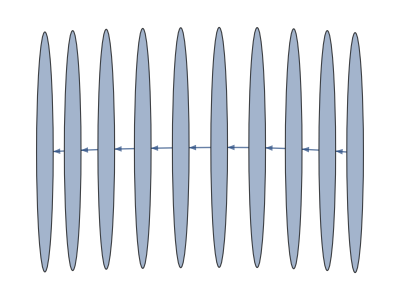
-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

Repeating

Repeating

{}

```mathematica
sss1b=SSS[4,20,SSSSize->{50,200},Max->10,NetSize->{400,300}, VertexSize->0.6];
sss1b["Verdict"]
GuessDimension[sss1b]
TestForUnusedRules[sss1b]
```

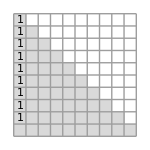
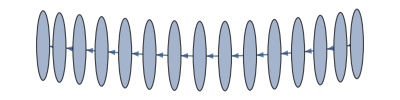
-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

OK

1D

{1D,{1,0,18,1},2
1,2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | }
{1D,{1,0,19,1},1
1,1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | }
{1D,{1,0,18,1},2
1,2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | }
{1D,{1,0,18,1},1
1,1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | }

1D

{}

```mathematica
sss20=SSS[20,20,SSSMax->10,SSSSize->{150,150},NetMax->15,NetSize->{400,100}, VertexSize->.8];
sss20["Verdict"]
GuessDimension[sss20]//Column
sss20["Verdict"]
TestForUnusedRules[sss20]
```

Note that GuessDimension has changed the "Verdict" field of sss20.

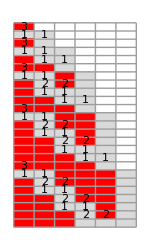



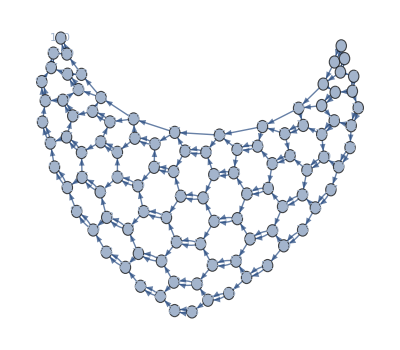
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

OK

2D

{2D,{1,0,5,2},7
5
2,7 | 12 | 19 | 28 | 39 | 52 | 67
5 | 7 | 9 | 11 | 13 | 15 | 
2 | 2 | 2 | 2 | 2 |  | }
{2D,{1,0,6,2},6
5
2,6 | 11 | 18 | 27 | 38 | 51 | 66 | 83
5 | 7 | 9 | 11 | 13 | 15 | 17 | 
2 | 2 | 2 | 2 | 2 | 2 |  | }
{2D,{1,0,6,2},5
5
2,5 | 10 | 17 | 26 | 37 | 50 | 65 | 82
5 | 7 | 9 | 11 | 13 | 15 | 17 | 
2 | 2 | 2 | 2 | 2 | 2 |  | }
{2D,{3,0,6,4/3},1 | 2 | 4
1 | 2 | 3
1 | 1 | 2,1 | 2 | 4 | 7 | 12 | 18 | 25 | 34 | 44 | 55
1 | 2 | 3 | 5 | 6 | 7 | 9 | 10 | 11 | 
1 | 1 | 2 | 1 | 1 | 2 | 1 | 1 |  | }

2D

```mathematica
sssHex=SSS[{"AA"->"BA","AB"->"AA","B"->"AA"},"B",100,SSSMax->25,SSSSize->{150,250},NetMax->100,NetSize->{400,350}, VertexSize->1];
sssHex["Verdict"]
GuessDimension[sssHex]//Column
sssHex["Verdict"]
```

```mathematica
TestForUnusedRules[sssHex]
```

{}

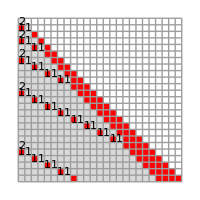
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

exp

{exp,{1,0,4,2},3
3
2,3 | 6 | 11 | 20 | 37 | 70 | 135 | 263
3 | 5 | 9 | 17 | 33 | 65 | 128 | 
2 | 4 | 8 | 16 | 32 | 63 |  | }
{exp,{1,0,6,2},1
2
1,1 | 3 | 6 | 11 | 20 | 37 | 70 | 135 | 264
2 | 3 | 5 | 9 | 17 | 33 | 65 | 129 | 
1 | 2 | 4 | 8 | 16 | 32 | 64 |  | }
{exp,{1,0,4,2},2
3
2,2 | 5 | 10 | 19 | 36 | 69 | 134
3 | 5 | 9 | 17 | 33 | 65 | 
2 | 4 | 8 | 16 | 32 |  | }
{exp,{2,0,4,2},1 | 2
1 | 2
1 | 1,1 | 2 | 4 | 7 | 13 | 24 | 46 | 89
1 | 2 | 3 | 6 | 11 | 22 | 43 | 
1 | 1 | 3 | 5 | 11 | 21 |  | }

exp

```mathematica
sssE=SSS[{"BA"->"AAB","A"->"BA"},"A",264,SSSMax->25,SSSSize->{200,200},NetSize->{400,300}, VertexLabels->None];
GuessDimension[sssE]//Column
sssE["Verdict"]
```

```mathematica
TestForUnusedRules[sssE]
```

{}

If the sessie grows exponentially, growth positions are probably frequent and unimportant.  Only cross-checking with the rule used, done by the included MergeIntervalsByRulesUsed, permits limiting consideration to significant positions.

```mathematica
Length[sssE["Evolution"]]
```

265

CheckDimension identifies the network as exponential soon as the sequence of ratios appears.  FixedPointList would continue until lines have zero length:

```mathematica
FixedPointList[Differences,MaxStateLengthPositions[sssE]]//Column
```

{3,6,11,20,37,70,135,263}
{3,5,9,17,33,65,128}
{2,4,8,16,32,63}
{2,4,8,16,31}
{2,4,8,15}
{2,4,7}
{2,3}
{1}
{}
{}

Interestingly, here the exponential behavior was only found in the DistanceTally data when running averages of pairs of integers were summed, the raw data is harder to recognize:

```mathematica
FixedPointList[Differences,DistanceTally[sssE]]//Column
```

{1,2,4,7,13,24,46,89}
{1,2,3,6,11,22,43}
{1,1,3,5,11,21}
{0,2,2,6,10}
{2,0,4,4}
{-2,4,0}
{6,-4}
{-10}
{}
{}

```mathematica
MovingAverage[#,2]& /@ FixedPointList[Differences,DistanceTally[sssE]][[;;-4]]//Column
```

{3/2,3,11/2,10,37/2,35,135/2}
{3/2,5/2,9/2,17/2,33/2,65/2}
{1,2,4,8,16}
{1,2,4,8}
{1,2,4}
{1,2}
{1}

### Testing

Still finding some bugs!

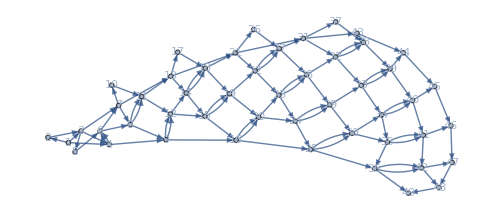
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sssTemp=SSS[{"AAB"->"AA","AA"->"ABA","B"->"A"},"AA",300,SSSMax->20,NetMax->49,SSSSize->100,NetSize->500];
```

```mathematica
$debug=False;
CheckDimension@MaxStateLengthPositions[sssTemp]
```

{2D,{1,0,13,2},5
5
2,5 | 10 | 17 | 26 | 37 | 50 | 65 | 82 | 101 | 122 | 145 | 170 | 197 | 226 | 257
5 | 7 | 9 | 11 | 13 | 15 | 17 | 19 | 21 | 23 | 25 | 27 | 29 | 31 | 
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 |  | }

```mathematica
CheckDimension@LeastUsedRulePositions[sssTemp]
```

{2D,{1,0,14,2},5
5
2,5 | 10 | 17 | 26 | 37 | 50 | 65 | 82 | 101 | 122 | 145 | 170 | 197 | 226 | 257 | 290
5 | 7 | 9 | 11 | 13 | 15 | 17 | 19 | 21 | 23 | 25 | 27 | 29 | 31 | 33 | 
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 |  | }

```mathematica
CheckDimension@DistanceTally[sssTemp]
```

{2D,{4,0,12,3/2},1 | 4 | 8 | 13
3 | 4 | 5 | 7
1 | 1 | 2 | 2,1 | 4 | 8 | 13 | 20 | 29 | 39 | 50 | 63 | 78 | 94 | 111 | 130 | 151 | 173 | 196 | 221
3 | 4 | 5 | 7 | 9 | 10 | 11 | 13 | 15 | 16 | 17 | 19 | 21 | 22 | 23 | 25 | 
1 | 1 | 2 | 2 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 2 | 1 | 1 | 2 |  | }

```mathematica
CheckDimension@DistanceLastPositions[sssTemp]
```

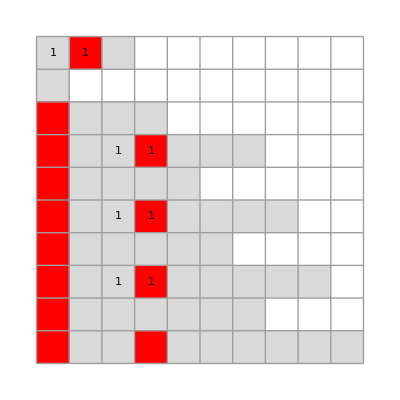
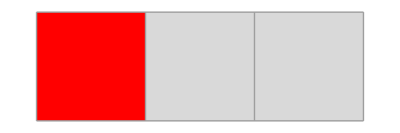
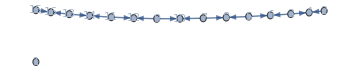
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
Clear[sssT];
sssT=SSS[15900,52,SSSSize->Tiny,NetSize->Medium,SSSMax->10,NetMax->16];
```

```mathematica
CheckDimension@MaxStateLengthPositions[sssT]
sssT["RulesUsed"]
CheckDimension@LeastUsedRulePositions[sssT]
```

{1D,{1,0,23,2},4
2,4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24 | 26 | 28 | 30 | 32 | 34 | 36 | 38 | 40 | 42 | 44 | 46 | 48 | 50
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | }

{1,2,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1}

{1D,{1,1,24,2},4
2,1 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24 | 26 | 28 | 30 | 32 | 34 | 36 | 38 | 40 | 42 | 44 | 46 | 48 | 50 | 52
3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | }

```mathematica
CheckDimension@DistanceTally[sssT]
```

{1D,{1,0,49,1},1
1,1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | }

```mathematica
sssT["Net"]
```

{3→4,2→4,5→6,3→6,7→8,5→8,9→10,7→10,11→12,9→12,13→14,11→14,15→16,13→16,17→18,15→18,19→20,17→20,21→22,19→22,23→24,21→24,25→26,23→26,27→28,25→28,29→30,27→30,31→32,29→32,33→34,31→34,35→36,33→36,37→38,35→38,39→40,37→40,41→42,39→42,43→44,41→44,45→46,43→46,47→48,45→48,49→50,47→50,51→52,49→52}

```mathematica
Keys[sssT]
```

{Net,OutDegreePotential,OutDegreeRemaining,OutDegreeActual,InDegree,ConnectionList,Verdict,RulesUsed,CellsDeleted,Distance,MaxColor,TagIndex,TEvolution,Evolution,RuleSet,TRuleSet,RuleSetWeight,RuleSetLength}

```mathematica
sssT["Distance"]
```

{0,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞}

```mathematica
ReliableDistances[sssT]
```

{2,1,0,4,3,6,5,8,7,10,9,12,11,14,13,16,15,18,17,20,19,22,21,24,23,26,25,28,27,30,29,32,31,34,33,36,35,38,37,40,39,42,41,44,43,46,45,48,47,50,49}

```mathematica
$debug=True;
ReliableDistances[sssT]
```

smallest node in net: 2

OutDegreeRemaining (massaged): {∞,∞,∞,∞,∞,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,2,0}

treating as zero (in odr): 0

using "OutDegreeRemaining" to find end of reliable data: {{∞,∞,∞,∞,∞,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,2},{0},{}}

Position of first untrustworthy node: {}

distances (uncut): {2,1,0,4,3,6,5,8,7,10,9,12,11,14,13,16,15,18,17,20,19,22,21,24,23,26,25,28,27,30,29,32,31,34,33,36,35,38,37,40,39,42,41,44,43,46,45,48,47,50,49}

last distance we'll trust: ∞

{2,1,0,4,3,6,5,8,7,10,9,12,11,14,13,16,15,18,17,20,19,22,21,24,23,26,25,28,27,30,29,32,31,34,33,36,35,38,37,40,39,42,41,44,43,46,45,48,47,50,49}

```mathematica
ReliableDistances[sssT]
```

{2,1,0,4,3,6,5,8,7,10,9,12,11,14,13,16,15,18,17,20,19,22,21,24,23,26,25,28,27,30,29,32,31,34,33,36,35,38,37,40,39,42,41,44,43,46,45,48,47}

```mathematica
sssT["Net"]
```

{3→4,2→4,5→6,3→6,7→8,5→8,9→10,7→10,11→12,9→12,13→14,11→14,15→16,13→16,17→18,15→18,19→20,17→20,21→22,19→22,23→24,21→24,25→26,23→26,27→28,25→28,29→30,27→30,31→32,29→32,33→34,31→34,35→36,33→36,37→38,35→38,39→40,37→40,41→42,39→42,43→44,41→44,45→46,43→46,47→48,45→48,49→50,47→50}

```mathematica
$debug=True;
ReliableDistances[sssT]
```

smallest node in net: 2

OutDegreeRemaining (massaged): {∞,∞,∞,∞,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,2,0}

treating as zero (in odr): 0

Position of first untrustworthy node: {}

distances (uncut): {2,1,0,4,3,6,5,8,7,10,9,12,11,14,13,16,15,18,17,20,19,22,21,24,23,26,25,28,27,30,29,32,31,34,33,36,35,38,37,40,39,42,41,44,43,46,45,48,47}

last distance we'll trust: ∞

{2,1,0,4,3,6,5,8,7,10,9,12,11,14,13,16,15,18,17,20,19,22,21,24,23,26,25,28,27,30,29,32,31,34,33,36,35,38,37,40,39,42,41,44,43,46,45,48,47}

```mathematica
$debug=True;
GuessDimension[sssT]
```

### Start of code to summarize Net:

```mathematica
ToNetDifferenceSets[net:{__Rule}] :=Module[{nodediffpairs},
nodediffpairs =  {#⟦1⟧,#⟦2⟧-#⟦1⟧}& /@ net;
Rest /@ 
Map[Last, 
Gather[Join[{#,0}& /@Range[Max[First/@nodediffpairs]],nodediffpairs],First[#1]==First[#2]&],
{2}]
];
FromNetDifferenceSets[diffs:{__List}] := Flatten[MapIndexed[Rule[First[#2],First[#2]+#1]&,diffs,{2}]];
ToNetDifferenceSets::usage ="ToNetDifferenceSets[net] takes a network given as a list of rules and returns a list of difference sets (sets of link lengths for each node) describing the same network.  A set {n1, n2, ...} in position i lists the indicates that net contained edges {i->n1, i->n2, ...}.";
FromNetDifferenceSets::usage ="FromNetDifferenceSets[l] takes a list l of sets of link lengths for each node of a network and returns the network described.  A set {n1, n2, ...} in position i of l corresponds to {i->n1, i->n2, ...} in the network.";
ToReducedNetDifferenceSets[l_List]:=SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}],
{x:PatternSequence[a:{___Integer}]}:>CenterDot[1,{a}]}];
ToReducedNetDifferenceSets::usage ="ToNetDifferenceSets[l] takes a list l of sets of link lengths for each node of a network and returns a reduced version in which duplicates or duplicate subsequences are summarized using the format n·{…}.";
```

*** Start here: recognize a row of net difference sets, by (?) "subtracting" with various offsets, identifying case with most 0 entries *)

```mathematica
ToReducedNetDifferenceSets@ToNetDifferenceSets@sss90["Net"]
```

{1·{{1,1,1}},1·{{1,3}},1·{{1,1,1}},1·{{1,1,2}},1·{{3,4}},1·{{1,1,1}},1·{{1,1,3}},1·{{1,1,4}},1·{{4,5}},1·{{1,1,1}},1·{{1,1,4}},2·{{1,1,5}},1·{{5,6}},1·{{1,1,1}},1·{{1,1,5}},3·{{1,1,6}},1·{{6,7}},1·{{1,1,1}},1·{{1,1,6}},4·{{1,1,7}},1·{{7,8}},1·{{1,1,1}},1·{{1,1,7}},5·{{1,1,8}},1·{{8,9}},1·{{1,1,1}},1·{{1,1,8}},6·{{1,1,9}},1·{{9,10}},1·{{1,1,1}},1·{{1,1,9}},7·{{1,1,10}},1·{{10,11}},1·{{1,1,1}},1·{{1,1,10}},8·{{1,1,11}},1·{{}},1·{{1,1,1}},8·{{1,1}}}

```mathematica
SetSubtract[1·{{1,3}},1·{{1,1,1}}]
```

{}

```mathematica
ToReducedNetDifferenceSets@ToNetDifferenceSets@sss90["Net"]
```

```mathematica
{1·{{1,1,1}},1·{{1,3}},1·{{1,1,1}},1·{{1,1,2}},1·{{3,4}},1·{{1,1,1}},1·{{1,1,3}},1·{{1,1,4}},1·{{4,5}},1·{{1,1,1}},1·{{1,1,4}},
2·{{1,1,5}},1·{{5,6}},1·{{1,1,1}},1·{{1,1,5}},
3·{{1,1,6}},1·{{6,7}},1·{{1,1,1}},1·{{1,1,6}},4·{{1,1,7}},1·{{7,8}},1·{{1,1,1}},1·{{1,1,7}},5·{{1,1,8}},1·{{8,9}},1·{{1,1,1}},1·{{1,1,8}},6·{{1,1,9}},1·{{9,10}},1·{{1,1,1}},1·{{1,1,9}},7·{{1,1,10}},1·{{10,11}},1·{{1,1,1}},1·{{1,1,10}},8·{{1,1,11}},1·{{}},1·{{1,1,1}},8·{{1,1}}}
```

```mathematica
Subtract[10,4]
```

6

```mathematica
With[{l = ToReducedNetDifferenceSets@ToNetDifferenceSets@sss90["Net"]},
Print[l[[5+8;;-1]]];
Print[l[[1+8;;-5]]];
Print[SetSubtract[l[[5+8;;-1]], l[[1+8;;-5]]]];
 Print[];
Table[SetSubtract[l[[k;;]], l[[;;-k]]], {k, 2, Length[l]/2}]
 ]
```

{1·{{5,6}},1·{{1,1,1}},1·{{1,1,5}},3·{{1,1,6}},1·{{6,7}},1·{{1,1,1}},1·{{1,1,6}},4·{{1,1,7}},1·{{7,8}},1·{{1,1,1}},1·{{1,1,7}},5·{{1,1,8}},1·{{8,9}},1·{{1,1,1}},1·{{1,1,8}},6·{{1,1,9}},1·{{9,10}},1·{{1,1,1}},1·{{1,1,9}},7·{{1,1,10}},1·{{10,11}},1·{{1,1,1}},1·{{1,1,10}},8·{{1,1,11}},1·{{}},1·{{1,1,1}},8·{{1,1}}}

{1·{{4,5}},1·{{1,1,1}},1·{{1,1,4}},2·{{1,1,5}},1·{{5,6}},1·{{1,1,1}},1·{{1,1,5}},3·{{1,1,6}},1·{{6,7}},1·{{1,1,1}},1·{{1,1,6}},4·{{1,1,7}},1·{{7,8}},1·{{1,1,1}},1·{{1,1,7}},5·{{1,1,8}},1·{{8,9}},1·{{1,1,1}},1·{{1,1,8}},6·{{1,1,9}},1·{{9,10}},1·{{1,1,1}},1·{{1,1,9}},7·{{1,1,10}},1·{{10,11}},1·{{1,1,1}},1·{{1,1,10}}}

{0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{∞,∞}},0·{{0,0,0}},7·{{0,0,∞}}}

{{0·{{0,2,∞}},0·{∞},0·{{0,0,1}},0·{{2,3,∞}},0·{∞},0·{{0,0,2}},0·{{0,0,1}},0·{{3,4,∞}},0·{∞},0·{{0,0,3}},1·{{0,0,1}},∞,0·{∞},0·{{0,0,4}},2·{{0,0,1}},∞,0·{∞},0·{{0,0,5}},3·{{0,0,1}},∞,0·{∞},0·{{0,0,6}},4·{{0,0,1}},∞,0·{∞},0·{{0,0,7}},5·{{0,0,1}},∞,0·{∞},0·{{0,0,8}},6·{{0,0,1}},∞,0·{∞},0·{{0,0,9}},7·{{0,0,1}},∞,0·{∞},7·{{0,0,∞}}},{0·{{0,0,0}},0·{∞},0·{{2,3,∞}},0·{{0,0,-1}},0·{∞},0·{{0,0,3}},0·{{3,4,∞}},0·{{0,0,-3}},0·{∞},1·{{0,0,4}},0·{{4,5,∞}},∞,0·{∞},2·{{0,0,5}},0·{{5,6,∞}},∞,0·{∞},3·{{0,0,6}},0·{{6,7,∞}},∞,0·{∞},4·{{0,0,7}},0·{{7,8,∞}},∞,0·{∞},5·{{0,0,8}},0·{{8,9,∞}},∞,0·{∞},6·{{0,0,9}},0·{{9,10,∞}},∞,0·{∞},7·{{0,0,10}},0·{{∞,∞,∞}},∞,7·{∞}},{0·{{0,0,1}},0·{{2,1}},0·{{0,0,0}},0·{{0,0,1}},0·{∞},0·{{3,4,∞}},0·{{0,0,-2}},0·{{0,0,0}},1·{∞},0·{{4,5,∞}},0·{{0,0,-3}},∞,2·{∞},0·{{5,6,∞}},0·{{0,0,-4}},∞,3·{∞},0·{{6,7,∞}},0·{{0,0,-5}},∞,4·{∞},0·{{7,8,∞}},0·{{0,0,-6}},∞,5·{∞},0·{{8,9,∞}},0·{{0,0,-7}},∞,6·{∞},0·{{9,10,∞}},0·{{0,0,-8}},∞,7·{∞},0·{{∞,∞,∞}},0·{{0,0,-9}},0·{{0,0,∞}}},{0·{{2,3,∞}},0·{∞},0·{{0,0,2}},0·{{0,0,2}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{∞,∞}},0·{{0,0,0}},7·{{0,0,∞}}},{0·{{0,0,0}},0·{∞},0·{{0,0,3}},0·{{3,4,∞}},0·{∞},0·{{0,0,3}},1·{{0,0,2}},0·{{4,5,∞}},0·{∞},0·{{0,0,4}},2·{{0,0,2}},∞,0·{∞},0·{{0,0,5}},3·{{0,0,2}},∞,0·{∞},0·{{0,0,6}},4·{{0,0,2}},∞,0·{∞},0·{{0,0,7}},5·{{0,0,2}},∞,0·{∞},0·{{0,0,8}},6·{{0,0,2}},∞,0·{∞},0·{{0,0,9}},7·{{0,0,2}},∞,0·{∞},7·{{0,0,∞}}},{0·{{0,0,2}},0·{∞},0·{{3,4,∞}},0·{{0,0,-1}},0·{∞},1·{{0,0,4}},0·{{4,5,∞}},0·{{0,0,-3}},0·{∞},2·{{0,0,5}},0·{{5,6,∞}},∞,0·{∞},3·{{0,0,6}},0·{{6,7,∞}},∞,0·{∞},4·{{0,0,7}},0·{{7,8,∞}},∞,0·{∞},5·{{0,0,8}},0·{{8,9,∞}},∞,0·{∞},6·{{0,0,9}},0·{{9,10,∞}},∞,0·{∞},7·{{0,0,10}},0·{{∞,∞,∞}},∞,7·{{-9,-10}}},{0·{{0,0,3}},0·{{3,2}},0·{{0,0,0}},0·{{0,0,2}},1·{∞},0·{{4,5,∞}},0·{{0,0,-2}},0·{{0,0,1}},2·{∞},0·{{5,6,∞}},0·{{0,0,-3}},∞,3·{∞},0·{{6,7,∞}},0·{{0,0,-4}},∞,4·{∞},0·{{7,8,∞}},0·{{0,0,-5}},∞,5·{∞},0·{{8,9,∞}},0·{{0,0,-6}},∞,6·{∞},0·{{9,10,∞}},0·{{0,0,-7}},∞,7·{∞},0·{{∞,∞,∞}},0·{{0,0,-8}},1·{{0,0,∞}}},{0·{{3,4,∞}},0·{∞},0·{{0,0,3}},1·{{0,0,3}},0·{{2,2}},0·{{0,0,0}},0·{{0,0,2}},2·{{0,0,2}},0·{{2,2}},0·{{0,0,0}},0·{{0,0,2}},2·{{0,0,2}},0·{{2,2}},0·{{0,0,0}},0·{{0,0,2}},2·{{0,0,2}},0·{{2,2}},0·{{0,0,0}},0·{{0,0,2}},2·{{0,0,2}},0·{{2,2}},0·{{0,0,0}},0·{{0,0,2}},2·{{0,0,2}},0·{{2,2}},0·{{0,0,0}},0·{{0,0,2}},2·{{0,0,2}},0·{{∞,∞}},0·{{0,0,0}},7·{{0,0,∞}}},{0·{{0,0,0}},0·{∞},1·{{0,0,4}},0·{{4,5,∞}},0·{∞},0·{{0,0,4}},2·{{0,0,3}},0·{{5,6,∞}},0·{∞},0·{{0,0,5}},3·{{0,0,3}},∞,0·{∞},0·{{0,0,6}},4·{{0,0,3}},∞,0·{∞},0·{{0,0,7}},5·{{0,0,3}},∞,0·{∞},0·{{0,0,8}},6·{{0,0,3}},∞,0·{∞},0·{{0,0,9}},7·{{0,0,3}},∞,0·{∞},7·{{0,0,∞}}},{0·{{0,0,3}},1·{∞},0·{{4,5,∞}},0·{{0,0,-1}},0·{∞},2·{{0,0,5}},0·{{5,6,∞}},0·{{0,0,-3}},0·{∞},3·{{0,0,6}},0·{{6,7,∞}},∞,0·{∞},4·{{0,0,7}},0·{{7,8,∞}},∞,0·{∞},5·{{0,0,8}},0·{{8,9,∞}},∞,0·{∞},6·{{0,0,9}},0·{{9,10,∞}},∞,0·{∞},7·{{0,0,10}},0·{{∞,∞,∞}},∞,7·{{-8,-9}}},{1·{{0,0,4}},0·{{4,3}},0·{{0,0,0}},0·{{0,0,3}},2·{∞},0·{{5,6,∞}},0·{{0,0,-2}},0·{{0,0,2}},3·{∞},0·{{6,7,∞}},0·{{0,0,-3}},∞,4·{∞},0·{{7,8,∞}},0·{{0,0,-4}},∞,5·{∞},0·{{8,9,∞}},0·{{0,0,-5}},∞,6·{∞},0·{{9,10,∞}},0·{{0,0,-6}},∞,7·{∞},0·{{∞,∞,∞}},0·{{0,0,-7}},2·{{0,0,∞}}},{0·{{4,5,∞}},0·{∞},0·{{0,0,4}},2·{{0,0,4}},0·{{3,3}},0·{{0,0,0}},0·{{0,0,3}},3·{{0,0,3}},0·{{3,3}},0·{{0,0,0}},0·{{0,0,3}},3·{{0,0,3}},0·{{3,3}},0·{{0,0,0}},0·{{0,0,3}},3·{{0,0,3}},0·{{3,3}},0·{{0,0,0}},0·{{0,0,3}},3·{{0,0,3}},0·{{3,3}},0·{{0,0,0}},0·{{0,0,3}},3·{{0,0,3}},0·{{∞,∞}},0·{{0,0,0}},7·{{0,0,∞}}},{0·{{0,0,0}},0·{∞},2·{{0,0,5}},0·{{5,6,∞}},0·{∞},0·{{0,0,5}},3·{{0,0,4}},0·{{6,7,∞}},0·{∞},0·{{0,0,6}},4·{{0,0,4}},∞,0·{∞},0·{{0,0,7}},5·{{0,0,4}},∞,0·{∞},0·{{0,0,8}},6·{{0,0,4}},∞,0·{∞},0·{{0,0,9}},7·{{0,0,4}},∞,0·{∞},7·{{0,0,∞}}},{0·{{0,0,4}},2·{∞},0·{{5,6,∞}},0·{{0,0,-1}},0·{∞},3·{{0,0,6}},0·{{6,7,∞}},0·{{0,0,-3}},0·{∞},4·{{0,0,7}},0·{{7,8,∞}},∞,0·{∞},5·{{0,0,8}},0·{{8,9,∞}},∞,0·{∞},6·{{0,0,9}},0·{{9,10,∞}},∞,0·{∞},7·{{0,0,10}},0·{{∞,∞,∞}},∞,7·{{-7,-8}}},{2·{{0,0,5}},0·{{5,4}},0·{{0,0,0}},0·{{0,0,4}},3·{∞},0·{{6,7,∞}},0·{{0,0,-2}},0·{{0,0,3}},4·{∞},0·{{7,8,∞}},0·{{0,0,-3}},∞,5·{∞},0·{{8,9,∞}},0·{{0,0,-4}},∞,6·{∞},0·{{9,10,∞}},0·{{0,0,-5}},∞,7·{∞},0·{{∞,∞,∞}},0·{{0,0,-6}},3·{{0,0,∞}}},{0·{{5,6,∞}},0·{∞},0·{{0,0,5}},3·{{0,0,5}},0·{{4,4}},0·{{0,0,0}},0·{{0,0,4}},4·{{0,0,4}},0·{{4,4}},0·{{0,0,0}},0·{{0,0,4}},4·{{0,0,4}},0·{{4,4}},0·{{0,0,0}},0·{{0,0,4}},4·{{0,0,4}},0·{{4,4}},0·{{0,0,0}},0·{{0,0,4}},4·{{0,0,4}},0·{{∞,∞}},0·{{0,0,0}},7·{{0,0,∞}}},{0·{{0,0,0}},0·{∞},3·{{0,0,6}},0·{{6,7,∞}},0·{∞},0·{{0,0,6}},4·{{0,0,5}},0·{{7,8,∞}},0·{∞},0·{{0,0,7}},5·{{0,0,5}},∞,0·{∞},0·{{0,0,8}},6·{{0,0,5}},∞,0·{∞},0·{{0,0,9}},7·{{0,0,5}},∞,0·{∞},7·{{0,0,∞}}},{0·{{0,0,5}},3·{∞},0·{{6,7,∞}},0·{{0,0,-1}},0·{∞},4·{{0,0,7}},0·{{7,8,∞}},0·{{0,0,-3}},0·{∞},5·{{0,0,8}},0·{{8,9,∞}},∞,0·{∞},6·{{0,0,9}},0·{{9,10,∞}},∞,0·{∞},7·{{0,0,10}},0·{{∞,∞,∞}},∞,7·{{-6,-7}}}}

```mathematica
Clear[SetSubtract];
SetSubtract[s2:{___Integer},s1:{___Integer}] := Module[{len1,len2},
If[(len1=Length[s1])<(len2=Length[s2]),∞,Join[s2-s1⟦1;;len2⟧,Table[∞,len1-len2]]]];
SetSubtract[(n2_Integer)·(s2:{{___Integer}..}),(n1_Integer)·(s1:{{___Integer}..})] := Module[{len1,len2},
Which[
n1>n2,∞,
(len1=Length[s1])<(len2=Length[s2]),∞,
True,(n2-n1)·Join[SetSubtract[s2,s1⟦1;;len2⟧],Table[∞,len1-len2]]
]];
SetSubtract[l2_List,l1_List] := 
If[Length[l1]==Length[l2],MapThread[SetSubtract,{l2,l1}]];
SetSubtract::usage="SetSubtract[s1,s2] or SetSubtract[n1·s1,n2·s2] performs a strange sort of 'set subtraction', in which elements of s2 are subtracted in order from the corresponding elements of s1, if the set sizes are the same, so SetSubtract[{1,4,9},{1,2,3}] gives {0,2,6}.  If s1 is longer than s2, the value ∞ is returned, if s2 is longer than s1, elements are subtracted until they run out, and the remaining subtractions return ∞. If n1>n2, the difference is given in the response, otherwise the entire expression returns ∞.";
```

```mathematica
SetSubtract[{1,2,3},{1,2,3,5}]
```

{0,0,0,∞}

```mathematica
SetSubtract[{1,2,3},{1,2}]
```

∞

```mathematica
SetSubtract[3·{{1,2,4}},1·{{1,2,3}}]
```

2·{{0,0,1}}

```mathematica
SetSubtract[{1,3,7},{1,2,3}]
```

{0,1,4}

```mathematica
With[{l = ToNetDifferenceSets[sss1a["Net"]]},
 Table[SetSubtract[l[[k ;;]], l[[;; -k]]], {k, 2, Length[l]/2}]
 ]
```

{{{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞},{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}},{{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞},{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}},{{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞},{{0},{},{0},{},{0},{},{0},{},{0},{},{0}},{{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞}}

```mathematica
First@MaximalBy[MapIndexed[{Count[#1,0,∞],First@#2,#1}&,%377,1],First]
```

{8,2,{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}}

```mathematica
With[{l = ToNetDifferenceSets[sss1a["Net"]]},
 Table[SetSubtract[l[[k ;;]], l[[;; -k]]], {k, 2, Length[l]/2}]
 ]
```

```mathematica
MapIndexed[{Count[#1,0,∞],First@#2,#1}&,%240,1]
```

{{0,1,{∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞}}},{8,2,{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}},{0,3,{∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞}}},{7,4,{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}},{0,5,{∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞}}},{6,6,{{0},{},{0},{},{0},{},{0},{},{0},{},{0}}},{0,7,{∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞}}}}

```mathematica
First@MaximalBy[MapIndexed[{Count[#1,0,∞],First@#2,#1}&,%240,1],First]
```

{8,2,{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}}

```mathematica
Count[{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}},_?AtomQ,∞]
```

8

```mathematica
With[{l={{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}},
SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}],
{x:PatternSequence[a:{___Integer}]}:>CenterDot[1,{a}]
}]]
```

{7·{{0},{}},1·{{0}}}

```mathematica
With[{l={{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}},
SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}]
}]]
```

{7·{{0},{}},{0}}

```mathematica
idMatch[{x___,(reps_Integer)·(match_List),z___}] := {Length[{x}],reps,match,Length[{z}]};
```

```mathematica
With[{l={{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}},
SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}]
}]] // idMatch
```

{0,7,{{0},{}},1}

```mathematica
RecognizeNet[sss_Association /; KeyExistsQ[sss,"Net"]] := 
Module[{netdiffs=ToNetDifferenceSets[sss["Net"]],
```

```mathematica
With[{l={{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}},
SequencePosition[l,
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]},Overlaps->False
]
]
```

{{1,14}}

```mathematica
RecognizeNetDifferences[l_List] := Module[{tbl,offst,cnt,ptrn,ttl,dlay,repcnt,mtch,xcs},
(* table of set differences for all offsets *)
tbl=Table[SetSubtract[l[[k;;]],l[[;;-k]]],{k,2,Length[l]/2}];
(* find count, offset and matched pattern for the best one = most 0s *)
{cnt,offst,ptrn}=First@MaximalBy[MapIndexed[{Count[#1,0,∞],First@#2,#1}&,tbl,1],First];
Print[{cnt,offst,ptrn}];
ttl=Count[ptrn,_?AtomQ,∞]; (* maximum number of 0s possible *)
If[cnt/ttl≥0.9 , (* covers 90% of the cases *)

{dlay,repcnt,mtch,xcs}=idMatch@SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}]
}] ;

Print[{dlay,repcnt,mtch,xcs}];
Return[{ToString[100*cnt/ttl]<>"%",{offst,dlay,repcnt,mtch,xcs}}]  (* after dlay *)
]];
RecognizeNetDifferences@ToNetDifferenceSets[sss1a["Net"]]
```

{8,2,{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}}

{0,8,{{1},{}},1}

{100%,{2,0,8,{{1},{}},1}}

```mathematica
RecognizeNetDifferences[l_List] := Module[{tbl,offst,cnt,ptrn,ttl,dlay,repcnt,mtch,xcs},
(* table of set differences for all offsets *)
tbl=Table[SetSubtract[l[[k;;]],l[[;;-k]]],{k,2,Length[l]/2}];
(* find count, offset and matched pattern for the best one = most 0s *)
{cnt,offst,ptrn}=First@MaximalBy[MapIndexed[{Count[#1,_?NonNegative,∞],First@#2,#1}&,tbl,1],First];
Print[{cnt,offst,ptrn}];
ttl=Count[ptrn,_?AtomQ,∞]; (* maximum number of 0s possible *)
If[cnt/ttl≥0.9 , (* covers 90% of the cases *)

{dlay,repcnt,mtch,xcs}=idMatch@SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}]
}] ;

Print[{dlay,repcnt,mtch,xcs}];
Return[{ToString[100.*cnt/ttl]<>"%",{offst,dlay,repcnt,mtch,xcs}}]  (* after dlay *)
]];
RecognizeNetDifferences@ToReducedNetDifferenceSets@ToNetDifferenceSets[sss90["Net"]]
```

{135,4,{0·{{2,3,∞}},0·{∞},0·{{0,0,2}},0·{{0,0,2}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{∞,∞}},0·{{0,0,0}},7·{{0,0,∞}}}}

{0,1,{{1,1,1}},38}

{103.846%,{4,0,1,{{1,1,1}},38}}

```mathematica
With[{ptrn={{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}},
MatchQ[ptrn,{Repeated[__,{0,5}],Longest[Repeated[b__,{5,∞}]],Repeated[__,{0,3}]}]
]
```

True

```mathematica
RecognizeNetSetDifferenceRow[l:((_List)..)] := Module[{len=Length[l],ptrn,dlay,mtch,k},

For[k=1,k≤len/2,k++,  (* for each possible offset size k *)
ptrn=MovingAverage[l,k];
If[MatchQ[ptrn,{Repeated[_,{0,5}],Repeated[b_,{5,∞}],Repeated[_,{0,3}]}],
(* accept no more than 5 junk items at the start, no more than 3 at the end, need at least 5 repeated items between *)
{dlay,mtch}=(ptrn/.{a:Repeated[_,{0,5}],Repeated[b_,{5,∞}],Repeated[_,{0,3}]}:>{Length[{a}],b}); 
Return[{"dim",{k,dlay,mtch}}]  (* dimension k, after dlay *)
];
];
{}]  (* {} = failure, {"dim", {k,dlay,(diff|ratio)mtch}} = success! *)
```

Clear[SubtractSetLists];
SubtractSetLists[s1_List, s2_List] := Module[{len1, len2},
   MapThread[If[(len1 = Length[#1]) < (len2 = Length[#2]), ∞, Join[#2 - #1[[1 ;; len2]], Table[∞, len1 - len2]]] &, {s1, s2}]
   ];

With[{l = ToNetDifferenceSets[sss1a["Net"]]},
 Table[SubtractSetLists[l[[k ;;]], l[[;; -k]]], {k, 2, Length[l]/2}]
 ]

{{∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞}},{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}},{∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞}},{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}},{∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞}},{{0},{},{0},{},{0},{},{0},{},{0},{},{0}},{∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞}}}

```mathematica
Count[#,0,∞]& /@ %219
```

{0,8,0,7,0,6,0}